```mathematica
(* Jonathan Foley *)

(* 
   Two State Transcription Model
rates per hour
 a==Promoter on rate
 b==Promoter off rate
 c==Transcription rate
 d==RNA degradation rate
*)

(*Define distribution*)

twoState/:PDF[twoState[a_,b_,c_,d_],x_]:=(Gamma[a/d+x]/(Gamma[x+1]*Gamma[a/d+b/d+x])*(Gamma[a/d+b/d]/Gamma[a/d])(c/d)^x*Hypergeometric1F1[a/d+x,a/d+b/d+x,-c/d]);twoState/:DistributionDomain[twoState[a_,b_,c_,d_]]:=Interval[{0,Infinity}];
twoState/:DistributionParameterAssumptions[twoState[a_,b_,c_,d_]]:=Element[{a,b,c,d},Reals]&&a>0&&b>0&&c>0&&d>0;
twoState/:DistributionParameterQ[twoState[a_,b_,c_,d_]]:=!TrueQ[Not[Element[{a,b,c,d},Reals]&&a>0&&b>0&&c>0&&d>0]]

(*define functions for fitting, custom distribution so can't use built in
functions *)


twoState/:LogLikelihood[twoState[a_,b_,c_,d_],data_]:=Sum[Evaluate[Log[PDF[twoState[a,b,c,d],x]]],{x,data}]

mle[data_]:=NArgMin[{-LogLikelihood[twoState[a,b,60,0.23],data],Element[{a,b},Reals]&&a>0&&b>0},{a,b}];

(* Import transcript counts, change directory as needed*)

(*SetDirectory["/Users/jonathan/Desktop/LGM2_AllClones_fitting/FISH_data3/"];*)
SetDirectory["/Users/jonathan/fitting/FISH_data3a/"];
files=FileNames["*.mat"];

data={};
names={};
importData[file_String]:=Block[{clone},
clone=Flatten[Import[file,"Data"]];
cloneName=StringSplit[file,"."][[1]];
data=Append[data,clone];
names=Append[names,cloneName];
]

Scan[importData,files]
```

```mathematica
names
```

{LGM2_A10,LGM2_A9,LGM2_AD1,LGM2_BC6,LGM2_C4,LGM2_CA1,LGM2_CA2,LGM2_CD2,LGM2_DB1,LGM2_DD3,LGM2_EB2,LGM2_EC5,LGM2_FA1,LGM2_FA2,LGM2_FA6,LGM2_FC5,LGM2_GA2,LGM2_GD1,LGM2_GD3,LGM2_H9,LGM2_HA4,LGM2_IB4,LGM2_IC4,LGM2_ID3,LGM2_ID5}

```mathematica
names[[12]]
```

LGM2_EC5

```mathematica
(* Compute mle fits *)
```

```mathematica
fitparams=ParallelMap[mle,data]
```

```mathematica
fitparams={{0.7725064389881605,22.87022024007231},{0.5473896761145638,28.402527411778138},{0.4184516380813457,23.287990726134378},{0.5098838429518049,3.027674029938454},{0.1970264153873515,5.305319227309268},{0.5988712138723115,8.372802544774993},{0.7012629681679303,24.967184386749043},{0.2781184401094418,11.74051252530304},{0.3485702818828408,13.908551745064543},{0.2959251879842593,9.552882468646818},{0.5284458132072373,34.80299970685725},{0.5926376666130447,32.75893944562971},{0.4555283979909465,33.1243832303662},{0.4992163880486545,10.899614509064122},{0.47381515221801895,16.97558982758685},{0.25660963076005683,10.125006804504478},{0.4080912261526899,3.6841907002101126},{0.4640914423958231,23.80323639838611},{0.2512043197504599,6.6788977748317135},{0.16142898935445446,8.144419785945214},{0.6075888088209789,7.940804291469481},{0.7625681988550975,9.694272943187528},{0.16510695879323992,2.9479774074868734},{0.9931079954053214,19.77897743259574}};
```

```mathematica
EC5fitparams={0.3198354585806007,11.24369271106979}
```

{0.319835,11.2437}

```mathematica
fitparams=Insert[fitparams,EC5fitparams,12]
```

{{0.772506,22.8702},{0.54739,28.4025},{0.418452,23.288},{0.509884,3.02767},{0.197026,5.30532},{0.598871,8.3728},{0.701263,24.9672},{0.278118,11.7405},{0.34857,13.9086},{0.295925,9.55288},{0.528446,34.803},{0.319835,11.2437},{0.592638,32.7589},{0.455528,33.1244},{0.499216,10.8996},{0.473815,16.9756},{0.25661,10.125},{0.408091,3.68419},{0.464091,23.8032},{0.251204,6.6789},{0.161429,8.14442},{0.607589,7.9408},{0.762568,9.69427},{0.165107,2.94798},{0.993108,19.779}}

```mathematica
(* Extract a and b *)
```

```mathematica
afit=fitparams[[All,1]];
bfit=fitparams[[All,2]];
```

```mathematica
Dimensions[data][[1]]
```

25

```mathematica
minLL=ParallelTable[LogLikelihood[twoState[afit[[i]],bfit[[i]],60,0.23],data[[i]]],{i,1,Dimensions[data][[1]]}]
```

{-1032.28,-613.057,-1285.75,-3677.18,-682.798,-3810.42,-3034.46,-1382.78,-2071.89,-1441.52,-2136.46,-2465.24,-2659.45,-422.017,-3572.1,-2303.21,-1992.3,-2145.87,-2323.79,-1205.83,-1265.25,-1399.63,-1616.86,-1989.24,-1835.97}

```mathematica
(*Compute 95% confidence intervals *)

amin=Table[NRoots[(LogLikelihood[twoState[a,bfit[[i]],60,0.23],data[[i]]]-minLL[[i]])/minLL[[i]]==0.05,{a,afit[[i]]-0.1*afit[[i]]}],{i,1,Dimensions[data][[1]]}];
amax=Table[FindRoot[(LogLikelihood[twoState[a,bfit[[i]],60,0.23],data[[i]]]-minLL[[i]])/minLL[[i]]==0.05,{a,afit[[i]]+0.1*afit[[i]]}],{i,1,Dimensions[data][[1]]}];

bmin=Table[FindRoot[(LogLikelihood[twoState[afit[[i]],b,60,0.23],data[[i]]]-minLL[[i]])/minLL[[i]]==0.05&&b>0,{b,bfit[[i]]-0.1*bfit[[i]]}],{i,1,Dimensions[data][[1]]}];
bmax=Table[FindRoot[(LogLikelihood[twoState[afit[[i]],b,60,0.23],data[[i]]]-minLL[[i]])/minLL[[i]]==0.05,{b,bfit[[i]]+0.1*bfit[[i]]}],{i,1,Dimensions[data][[1]]}];
```

```mathematica
amin=ParallelTable[NRoot[-LogLikelihood[twoState[a,bfit[[i]],60,0.23],data[[i]]]+minLL[[i]]==1.92,{a,afit[[i]]-0.1*afit[[i]]}],{i,1,25}];
amax=ParallelTable[NRoot[-LogLikelihood[twoState[a,bfit[[i]],60,0.23],data[[i]]]+minLL[[i]]==1.92,{a,afit[[i]]+0.1*afit[[i]]}],{i,1,25}];
bmin=ParallelTable[NRoot[-LogLikelihood[twoState[afit[[i]],b,60,0.23],data[[i]]]+minLL[[i]]==1.92,{b,bfit[[i]]-0.1*bfit[[i]]}],{i,1,25}];
bmax=ParallelTable[NRoot[-LogLikelihood[twoState[afit[[i]],b,60,0.23],data[[i]]]+minLL[[i]]==1.92,{b,bfit[[i]]+0.1*bfit[[i]]}],{i,1,25}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

$Aborted

$Aborted

```mathematica
LogLikelihood[twoState[afit[[24]],b,60,0.23],data[[24]]]/.bmin[[24]]
```

-2088.7

```mathematica
minLL[[24]]
```

{{0.241556,0.287675},{0.187478,0.230449},{0.153629,0.192536},{0.201921,0.251885},{0.0877508,0.11829},{0.210247,0.253804},{0.225171,0.270509},{0.114127,0.14783},{0.135165,0.171225},{0.120398,0.15477},{0.183905,0.227812},{0.127498,0.162818},{0.199318,0.244189},{0.164027,0.205589},{0.180212,0.220607},{0.170416,0.210135},{0.107728,0.140694},{0.166625,0.210244},{0.166394,0.206629},{0.107798,0.141316},{0.0732101,0.100527},{0.212943,0.256873},{0.247716,0.293829},{0.0793472,0.110721},{0.288418,0.33723}}

```mathematica
(* collect deccriptive stats *)
```

```mathematica
mu=Map[Mean,data]
std=Map[StandardDeviation,data]
sk=Map[Skewness,data];
var=Map[Variance,data];
cv=std/mu
f=var/mu;
names
```

{8.52326,4.9322,4.60442,37.6942,9.33173,17.4304,7.12571,6.04149,6.37622,7.82328,3.90192,7.21691,4.63524,3.53889,11.4251,7.0844,6.45361,26.0117,4.98865,9.45082,5.07889,18.543,19.0414,13.9634,12.4725}

{5.48994,3.97166,4.06513,22.6184,10.5235,10.5358,5.0983,5.53484,5.82877,8.06447,3.16093,6.45082,3.68509,3.09688,8.2267,5.42985,6.12436,18.8105,4.18328,9.45162,5.80526,11.6221,10.2131,13.7419,6.7787}

{0.644113,0.805251,0.882876,0.600049,1.12771,0.604452,0.71548,0.916138,0.914141,1.03083,0.810098,0.893847,0.795016,0.875099,0.720057,0.766452,0.948982,0.723156,0.838561,1.00009,1.14302,0.626765,0.536362,0.984137,0.543493}

{LGM2_A10,LGM2_A9,LGM2_AD1,LGM2_BC6,LGM2_C4,LGM2_CA1,LGM2_CA2,LGM2_CD2,LGM2_DB1,LGM2_DD3,LGM2_EB2,LGM2_EC5,LGM2_FA1,LGM2_FA2,LGM2_FA6,LGM2_FC5,LGM2_GA2,LGM2_GD1,LGM2_GD3,LGM2_H9,LGM2_HA4,LGM2_IB4,LGM2_IC4,LGM2_ID3,LGM2_ID5}

```mathematica
(*bootstraps*)
skewstrap=Table[Table[Skewness[RandomChoice[data[[i]],Length[data[[i]]]]],{1000}],{i,Length[data]}];
meanstrap=Table[Table[Mean[RandomChoice[data[[i]],Length[data[[i]]]]],{1000}],{i,Length[data]}];
varstrap=Table[Table[Variance[RandomChoice[data[[i]],Length[data[[i]]]]],{1000}],{i,Length[data]}];


skew95=Table[Quantile[skewstrap[[i]],{.025,.975}],{i,Length[skewstrap]}];
mu95=Table[Quantile[meanstrap[[i]],{.025,.975}],{i,Length[skewstrap]}];
var95=Table[Quantile[varstrap[[i]],{.025,.975}],{i,Length[skewstrap]}];
```

```mathematica
Needs["ErrorBarPlots`"]
Table[{{mu[[i]],afit[[i]]/0.23},ErrorBar[aErrors[[i]]]},{i,1,25}]
(*Generate some linear fits and summary plots*)
```

{{{8.52326,3.35872},ErrorBar[{1.05025,1.25076}]},{{4.9322,2.37996},ErrorBar[{0.815124,1.00195}]},{{4.60442,1.81935},ErrorBar[{0.66795,0.837111}]},{{37.6942,2.21689},ErrorBar[{0.877919,1.09515}]},{{9.33173,0.856637},ErrorBar[{0.381525,0.514305}]},{{17.4304,2.60379},ErrorBar[{0.914119,1.1035}]},{{7.12571,3.04897},ErrorBar[{0.979002,1.17613}]},{{6.04149,1.20921},ErrorBar[{0.496204,0.64274}]},{{6.37622,1.51552},ErrorBar[{0.587672,0.744456}]},{{7.82328,1.28663},ErrorBar[{0.523468,0.672915}]},{{3.90192,2.29759},ErrorBar[{0.799587,0.990487}]},{{7.21691,1.39059},ErrorBar[{0.554338,0.707906}]},{{4.63524,2.57669},ErrorBar[{0.866601,1.06169}]},{{3.53889,1.98056},ErrorBar[{0.71316,0.893865}]},{{11.4251,2.17051},ErrorBar[{0.783532,0.959163}]},{{7.0844,2.06007},ErrorBar[{0.740941,0.91363}]},{{6.45361,1.11569},ErrorBar[{0.468383,0.611712}]},{{26.0117,1.77431},ErrorBar[{0.724458,0.914105}]},{{4.98865,2.01779},ErrorBar[{0.723452,0.898385}]},{{9.45082,1.09219},ErrorBar[{0.468687,0.614415}]},{{5.07889,0.701865},ErrorBar[{0.318305,0.437075}]},{{18.543,2.64169},ErrorBar[{0.925838,1.11684}]},{{19.0414,3.31551},ErrorBar[{1.07703,1.27752}]},{{13.9634,0.717856},ErrorBar[{0.344988,0.481394}]},{{12.4725,4.31786},ErrorBar[{1.25399,1.46622}]}}

FittedModel[1.79332+0.0213639 x]

0.0358748

FittedModel[2.44679-0.0662045 x]

0.151674

FittedModel[1.20131+0.499216 x]

0.566066

FittedModel[1.75876-0.0321144 x]

0.221059

FittedModel[0.612364+0.144703 x]

0.212891

FittedModel[0.172612+1.60831 x]

0.884753

FittedModel[0.0863059-0.195847 x]

0.312881

FittedModel[0.935657-0.0111695 x]

0.271877

FittedModel[5.81904-4.64681 x]

0.778806

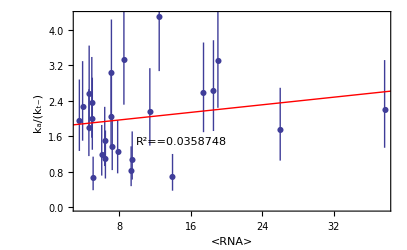

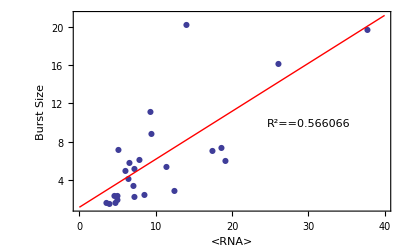

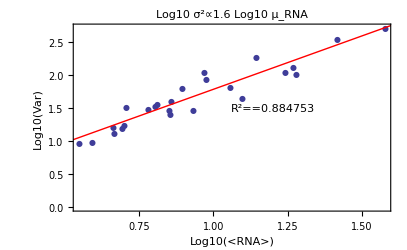

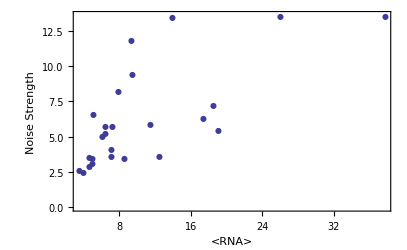

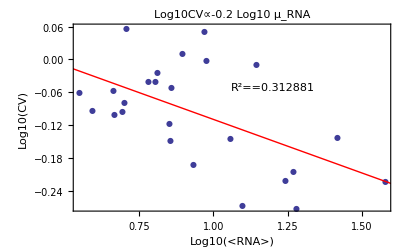

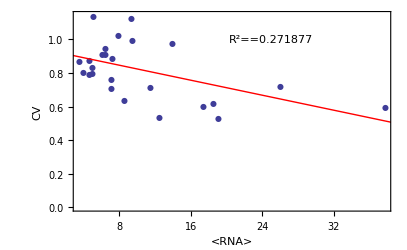

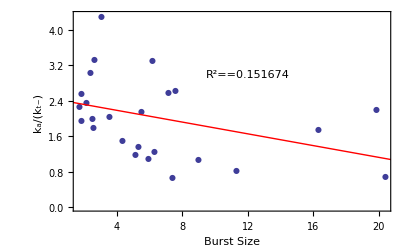

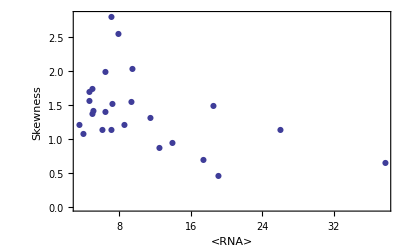

```mathematica
mukafit=LinearModelFit[Transpose[{mu,afit/0.23}],x,x]
mukafit["RSquared"]
kaBfit=LinearModelFit[Transpose[{60/bfit,afit/0.23}],x,x]
kaBfit["RSquared"]
muBfit=LinearModelFit[Transpose[{mu,60/bfit}],x,x]
muBfit["RSquared"]
muSKfit=LinearModelFit[Transpose[{mu,sk}],x,x]
muSKfit["RSquared"]
SKCVfit=LinearModelFit[Transpose[{sk,cv}],x,x]
SKCVfit["RSquared"]
LogMuVarfit=LinearModelFit[Transpose[{Log10[mu],Log10[var]}],x,x]
LogMuVarfit["RSquared"]
LogMuCVfit=LinearModelFit[Transpose[{Log10[mu],Log10[cv]}],x,x]
LogMuCVfit["RSquared"]
MuCVfit=LinearModelFit[Transpose[{mu,cv}],x,x]
MuCVfit["RSquared"]
CVkafit=LinearModelFit[Transpose[{cv,afit/0.23}],x,x]
CVkafit["RSquared"]


Show[ErrorListPlot[Table[{{mu[[i]],afit[[i]]/0.23},ErrorBar[aErrors[[i]]]},{i,1,25}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},Epilog->Inset[R^2==mukafit["RSquared"],{15,1.5}],FrameLabel->{"<RNA>","k_a/(k_(t-))"},RotateLabel->False,BaseStyle->{14,Bold}],Plot[mukafit["BestFit"],{x,0,40},PlotStyle->{Red}]]


Show[ListPlot[Transpose[{mu,60/bfit}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},Epilog->Inset[R^2==muBfit["RSquared"],{30,10}],FrameLabel->{"<RNA>","Burst Size"},PlotRange->All],Plot[muBfit["BestFit"],{x,0,40},PlotStyle->{Red}]]

Show[ListPlot[Transpose[{Log10[mu],Log10[var]}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},Epilog->Inset[R^2==LogMuVarfit["RSquared"],{1.2,1.5}],PlotLabel->Proportional[Log10 σ^2,1.6Log10 Subscript[μ, RNA]],FrameLabel->{"Log10(<RNA>)","Log10(Var)"}],Plot[LogMuVarfit["BestFit"],{x,-1,3},PlotStyle->{Red}]]

Show[ListPlot[Transpose[{mu,f}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"<RNA>","Noise Strength"}]]

Show[ListPlot[Transpose[{Log10[mu],Log10[cv]}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"Log10(<RNA>)","Log10(CV)"}],Plot[LogMuCVfit["BestFit"],{x,0.01,3},PlotStyle->{Red}],Epilog->Inset[R^2==LogMuCVfit["RSquared"],{1.2,-0.05}],PlotLabel->Proportional[Log10CV,-0.2Log10 Subscript[μ, RNA]]]

Show[ListPlot[Transpose[{mu,cv}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"<RNA>","CV"}],Plot[MuCVfit["BestFit"],{x,1,40},PlotStyle->{Red}],Epilog->Inset[R^2==MuCVfit["RSquared"],{25,1.0}]]

Show[ListPlot[Transpose[{60/bfit,afit/0.23}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},Epilog->Inset[R^2==kaBfit["RSquared"],{12,3}],BaseStyle->{14,Bold},FrameLabel->{"Burst Size","k_a/(k_(t-))"},RotateLabel->False],Plot[kaBfit["BestFit"],{x,0,40},PlotStyle->{Red}]]

Show[ListPlot[Transpose[{mu,sk}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"<RNA>","Skewness"}]]

Show[ListPlot[Transpose[{cv,sk}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"CV","Skewness"}]]

Show[ListPlot[Transpose[{cv,afit/0.23}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},BaseStyle->{14,Bold},Epilog->Inset[R^2==CVkafit["RSquared"],{0.7,1}],FrameLabel->{"CV","k_a/(k_(t-))"},RotateLabel->False],Plot[CVkafit["BestFit"],{x,0.5,1.5},PlotStyle->{Red}]]

Show[ListPlot[Transpose[{cv,60/bfit}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"CV","Burst Size"}]]

Show[ListPlot[Transpose[{sk,afit/0.23}],BaseStyle->{14,Bold},PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"Skewness","k_a/(k_(t-))"},RotateLabel->False]]

Show[ListPlot[Transpose[{sk,60/bfit}],PlotMarkers->{Automatic,8},Frame->{True,True,False,False},BaseStyle->{14,Bold},FrameLabel->{"Skewness","Burst Size"}]]
```

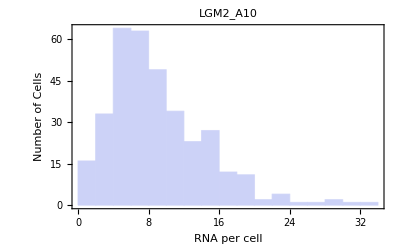
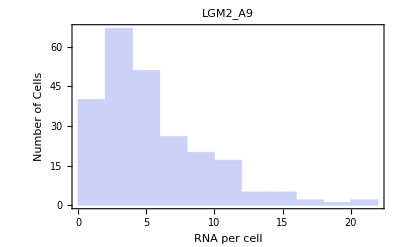
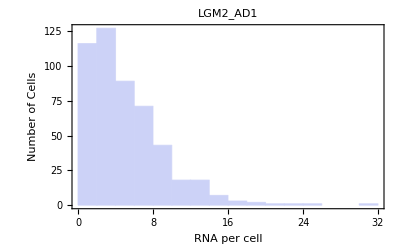
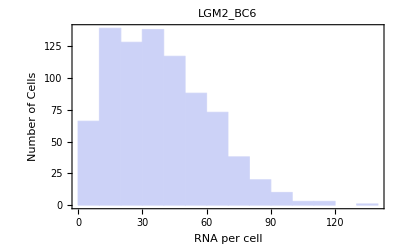
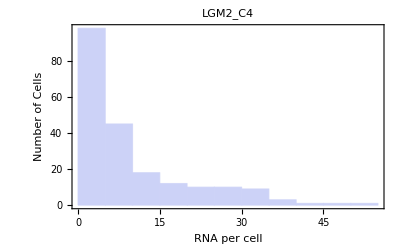
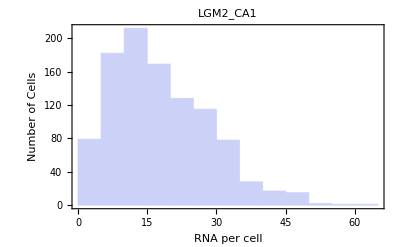
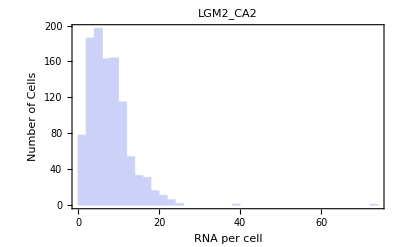
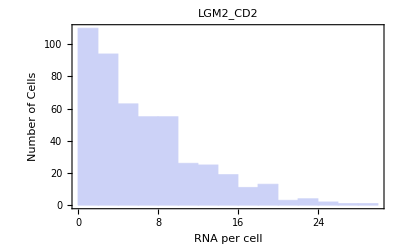

```mathematica
(* Plot histograms *)
ParallelTable[Histogram[data[[i]],PlotLabel->names[[i]],Frame->{True,True,False,False},FrameLabel->{"RNA per cell","Number of Cells"},PlotRange->All],{i,1,Length[data]}]
```

```mathematica
(*overlay histograms with fits*)
```

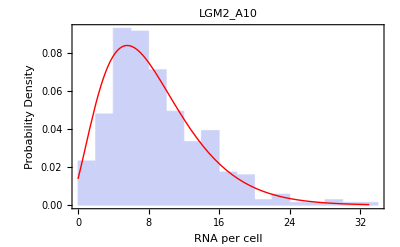
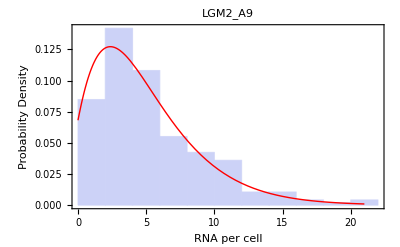
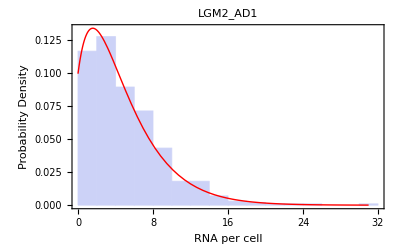
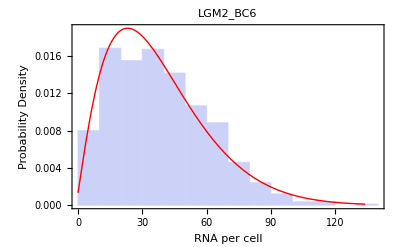
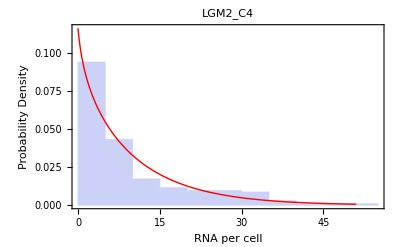
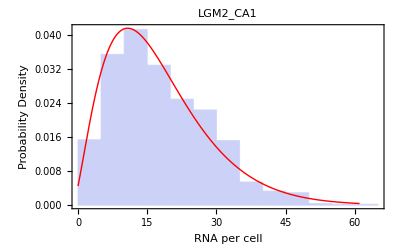
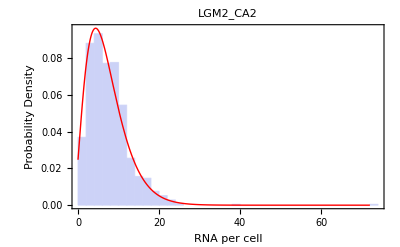
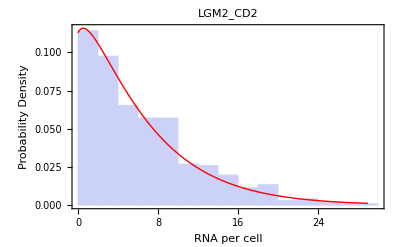

```mathematica
ParallelTable[Show[Histogram[data[[i]],Automatic,"PDF",PlotLabel->names[[i]],Frame->{True,True,False,False},FrameLabel->{"RNA per cell","Probability Density"}],Plot[PDF[twoState[afit[[i]],bfit[[i]],60,0.23],x],{x,0,Max[data[[i]]]},PlotStyle->{Red},PlotRange->All]],{i,1,Length[data]}]
```

```mathematica
Export["DistsWFits.pdf",%]
```

DistsWFits.pdf

```mathematica
ncells=Map[Length,data]
```

{344,236,498,824,208,1027,1058,482,715,464,887,816,1050,180,1061,782,679,513,881,366,469,372,435,546,563}

```mathematica
Total[ncells]
```

14640

```mathematica
cloneData={names,ncells,mu,var,cv,sk,f,afit,60.0/bfit};
Export["LGM2_NSA_revised042512.xls",Transpose[cloneData]];
```

```mathematica
s
```